# WellBeing Tracker Project

Goal: Use machine learning to help predict when people will feel stressed and be prone to making mistakes. It will look for patterns of mood and activities that the user inputs, identify stress factors, and send a reminder or warning message to the user when the algorithm determines it would be helpful.

New Focus: Notification Aspect of Mood tracking apps
http://web.mit.edu/bentley/www/papers/reminders-note-forAC.pdf
Apple watch apps from wolfram mathematica: http://blog.wolfram.com/2015/04/28/instant-apps-for-the-apple-watch-with-the-wolfram-language/

make an option with manipulate to go back and make scenarios where you can see how your week could hypothetically could have been if you for example you ate 1 more serving of fruit
“Second, users usually tend to self-report data after the event to be recorded has occurred. In fact,
often it is not feasible for the user to interrupt her activity in order to record what she feels.
However, when the user is reminded of reporting the data, it is often too late to recollect
the exact experienced emotional states”(Computers page 3)

Supporting users in the retrospective reconstruction of emotions. Since people’s reports of their
emotions reflect whatever information is accessible at the time [24], we aim to provide people with
some hints in order to recall the experience where the emotions arose. This would allow the user
to connect her emotional states to the places visited, the people met, and the task accomplished,
and, through them, remember what happened to her during the day and report her emotions
more faithfully, in a way as similar as possible to how it actually happened (trying to avoid the
influence of beliefs).(computers page 4)
loading page is a get request 

cloud deploy with an api functon

Data Entries:
Google Form for mood daily logs:
https://docs.google.com/forms/d/12bnXVh8ggOZ5qTDeQxSybTICTjNi1-iyq4XpFTgEZfY/viewform?c=0&w=1&edit_requested=true #responses

Need to learn about how to quantify stress, draw from existing mood apps, and clarify goal for this project
https://yalantis.com/blog/best-mood-tracking-mobile-apps-and-how-to-develop-one/

http://technori.com/2018/04/4281-the-beginners-guide-to-quantified-self-plus-a-list-of-the-best-personal-data-tools-out-there/

## Text/Sentiment Analysis

Take in sentences that people put in and use the dependency of words in an accumulated list to create correlations between sentiment and activities
Word embedding in context?

ELMo Contextual Word Representations Trained on 1B Word Benchmark: Represent words as contextual word-embedding vectors: 
	Produces three vectors per token, two of which are contextual, meaning that they depend on the entire sentence in which they are used. These word vectors are aimed at being linearly combined. They are based on the characters and case-sensitive, so there is no token dictionary.
https://resources.wolframcloud.com/NeuralNetRepository/resources/ELMo-Contextual-Word-Representations-Trained-on-1B-Word-Benchmark

Need to input the text, separate into sentences, and analyze sentiment holistically:

```mathematica
text="I am feeling peaceful. Watched the sun rise and heard the birds chirp a beautiful good morning song. I caught up on slack messages and smiled at the intellectual curiousity and genuine helpfulness of students and instructors working together to do something amazing. Being a part of such a wonderful, diverse group of people coming together regardless of differences in backgrounds, religion, race and gender is inspiring. Stretching sore muscles (body and brain) reminds me both have been worked, and it feels good.";
```

```mathematica
sentences = TextCases[text, "Sentence"]
```

{I am feeling peaceful.,Watched the sun rise and heard the birds chirp a beautiful good morning song.,I caught up on slack messages and smiled at the intellectual curiousity and genuine helpfulness of students and instructors working together to do something amazing.,Being a part of such a wonderful, diverse group of people coming together regardless of differences in backgrounds, religion, race and gender is inspiring.,Stretching sore muscles (body and brain) reminds me both have been worked, and it feels good.}

```mathematica
Map[PartOfSpeech,{"dog","eat"}][[2]][[1]]
```

verb

```mathematica
words = TextCases[text, "Word"]
```

{I,am,feeling,peaceful,Watched,the,sun,rise,and,heard,the,birds,chirp,a,beautiful,good,morning,song,I,caught,up,on,slack,messages,and,smiled,at,the,intellectual,curiousity,and,genuine,helpfulness,of,students,and,instructors,working,together,to,do,something,amazing,Being,a,part,of,such,a,wonderful,diverse,group,of,people,coming,together,regardless,of,differences,in,backgrounds,religion,race,and,gender,is,inspiring,Stretching,sore,muscles,body,and,brain,reminds,me,both,have,been,worked,and,it,feels,good}

```mathematica
(* Make list of how often sentences with activity names are classified as positive and negative and use the probability as a way of making a ranking system *)
(* for each sentence, classify as positive/neg/ind
then save the activities into 3 separate lists*)



(* Count occurrences neg, pos, neutral *)
```

```mathematica
Counts[Classify["Sentiment", sentences]]
```

<|Positive→4,Negative→1|>

```mathematica
PieChart[Counts[Classify["Sentiment", TextCases[text, "Sentence"]]]]
```

-Graphics-

```mathematica
countSentiments[ text ]
```

-Graphics-

```mathematica
Mean@Classify["Sentiment", sentences, "Probabilities"][[All,"Positive"]]
```

0.7445

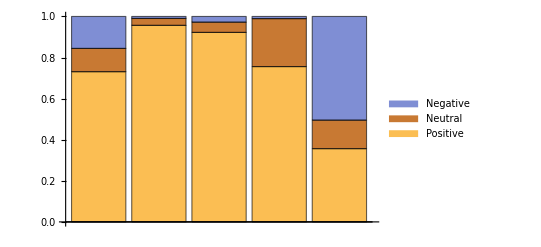

```mathematica
BarChart[Classify["Sentiment", sentences, "Probabilities"],
ChartLegends->Automatic,
ChartLayout->"Stacked"]
```

```mathematica
countSentiments[ text_String ] := With[{sentences = TextCases[text, "Sentence"]},
	   
	   PieChart[Counts[Classify["Sentiment", sentences]], ChartLabels -> Automatic]
	   
];
```

```mathematica
countSentiments["I am good. I like puppies."]
(* not printing out the counts.... *)
```

```mathematica
(* Count positive sentences and extract activities from those statements *)
```

```mathematica
countPositive[ text_String ] := Module[{sentences, words, positivePhrases},

	sentences = TextCases[text, "Sentence"];
	For[i = 0, i ≤ Length[sentences], i++, Classify["Sentiment",sentences[[i]], "Probabilities"];
	
	positivePhrases={};
		If["Sentiment" =="Positive", AppendTo[positivePhrases, sentence], Nothing]
		
			get list of activities and probability counts from sentence
			
				words = TextCases[text, "Word"];
				positiveWords = Map[PartOfSpeech,words][[i]][[1]];
				
	WHat to return: {{basketball,0.9},{reading,0.5},{....
					Occurrences of positive, negative, neutral sentences
```

```mathematica
(* make histogram of positive activities *)
```

```mathematica
(* make timeline plot of probability of positivity, negativity, and neutrality for each activity *)
```

```mathematica
ResourceObject["ELMo Contextual Word Representations Trained on 1B Word Benchmark"];
embeddings = NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"]
```

$Failed

```mathematica
Classify["Sentiment",
TextCases["I ate breakfast. I took a nap. I feel happy.","Sentence"],"Probabilities"]
```

{<|Positive→0.881403,Neutral→0.0890703,Negative→0.0295262|>,<|Positive→0.41956,Neutral→0.232822,Negative→0.347618|>,<|Positive→0.91959,Neutral→0.0201252,Negative→0.0602851|>}

```mathematica
ageForm = FormFunction[{"age"-> "String", "Resting Heart Rate" -> "Number"},f];
```

```mathematica
CloudDeploy[ageForm]
```

CloudObject[https://www.wolframcloud.com/objects/ed354240-93d2-452d-b7d5-afb84850fb3b]

```mathematica
<<HTTPHandling'
```

Get::noopen: Cannot open HTTPHandling.

$Failed'

```mathematica
StartWebServer[
FormFunction[{"age"-> "String", "Resting Heart Rate" -> "Number"},f]]
```

StartWebServer[FormFunction[]]

```mathematica
bin = CreateDatabin[];
CloudDeploy[FormFunction[
{"age"-> "String", "Resting Heart Rate" -> "Number"},
(DatabinAdd[bin];
"Thanks for submitting your data to Hearty! ")&]]
Dataset[bin]
```

CloudObject[https://www.wolframcloud.com/objects/4bdb5eba-68eb-4c8a-9bbd-00bff489c6ae]

Dataset[<>]

```mathematica
CloudObject[["https://www.wolframcloud.com/objects/019ce41d-0cfd-4c92-b90f-f5d16aa80fc2"](https://www.wolframcloud.com/objects/019ce41d-0cfd-4c92-b90f-f5d16aa80fc2)]
```

## Web Interface

```mathematica
bin = CreateDatabin[];
CloudDeploy[FormFunction[
{"age"-> "Integer", "Resting Heart Rate" -> "Number"}, targethr=(220-#age)*0.5&,
(DatabinAdd[bin];
"Thanks for submitting your data to Hearty! ")&]]
Dataset[bin]
```

CloudObject[https://www.wolframcloud.com/objects/dddc4bad-1bb3-497a-a494-ee056ee8431b]

Dataset[<>]

```mathematica
FormFunction[{"x"->Integer},#x^2&]
```

FormFunction[]

```mathematica
CloudDeploy[FormFunction[
{"age"-> "Integer", "Resting Heart Rate" -> "Number"},(targethr=(220-#age)*0.5;
StringJoin["Thanks for submitting your data to Hearty! ",targethr])&]]
```

CloudObject[https://www.wolframcloud.com/objects/f39c34d7-93b6-4559-a0da-381255645c8f]

```mathematica
FormFunction[{"p"-> Number,"r"->Integer},#p*#r&]
```

```mathematica
FormFunction[][<|"p"->5,"r"->3|>]
```

15

```mathematica
(#+2)&
```

#1+2&

```mathematica
Function[#+2][1,2]
```

3

```mathematica
Function[#1+#2+2][1,2]
```

5